```mathematica
y[x_] := m*x + c + ϵ
```

```mathematica
m = 100;
c =  500;
ϵ:= RandomVariate[NormalDistribution[0,50]]
```

```mathematica
Solve[CDF[NormalDistribution[0,1],X]==0.75,X]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{X→0.67449}}

```mathematica
CDF[NormalDistribution[0,1],-0.67449]
```

0.25

```mathematica
ϵ
```

28.7932

```mathematica
xx = Flatten[List[Table[-0.67449,{10}],Table[0.67449,{10}]]];
```

```mathematica
yy=Map[y,xx]
```

{435.897,408.995,490.911,523.444,433.357,484.178,459.696,459.818,432.333,431.217,544.38,491.582,627.665,552.663,663.439,567.834,589.357,440.123,617.561,608.187}

```mathematica
zz=Thread[{xx,yy}]
```

{{-0.67449,435.897},{-0.67449,408.995},{-0.67449,490.911},{-0.67449,523.444},{-0.67449,433.357},{-0.67449,484.178},{-0.67449,459.696},{-0.67449,459.818},{-0.67449,432.333},{-0.67449,431.217},{0.67449,544.38},{0.67449,491.582},{0.67449,627.665},{0.67449,552.663},{0.67449,663.439},{0.67449,567.834},{0.67449,589.357},{0.67449,440.123},{0.67449,617.561},{0.67449,608.187}}

```mathematica
model = LinearModelFit[zz,xxx,xxx]
```

FittedModel[513.132+84.7266 xxx]

```mathematica
model["BestFit"]
```

513.132+84.7266 xxx

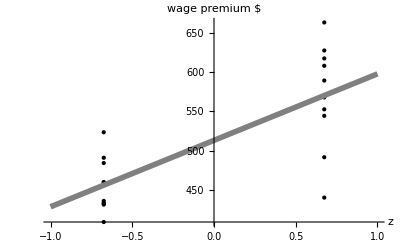

```mathematica
Show[ListPlot[zz,PlotRange->{{-1,1},Automatic},AxesLabel->{z,"wage premium $"},BaseStyle->{FontSize->16},PlotStyle->{Black}],Plot[model["BestFit"],{xxx,-1,1},PlotRange->{{0,1},Automatic},PlotStyle->{Gray,Thickness[0.01]}]]
```

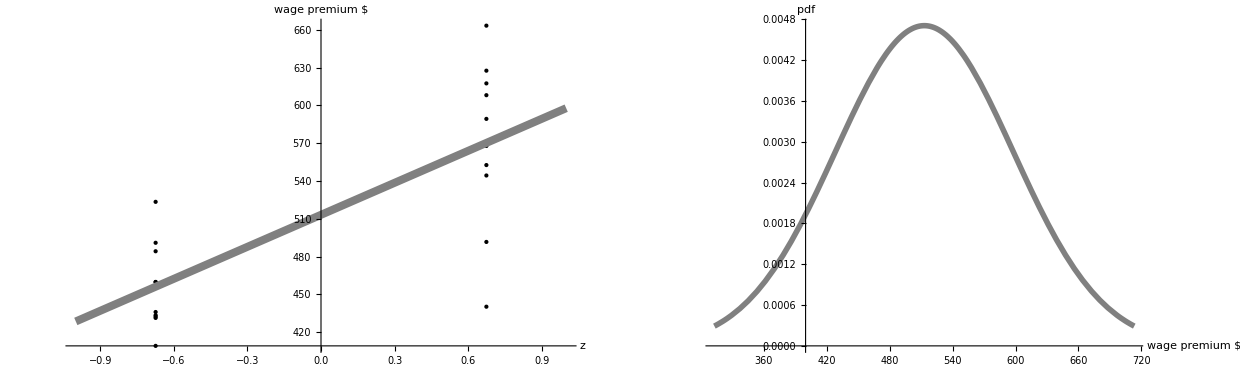

```mathematica
GraphicsRow[{Show[%269,ImageSize->Large],Plot[PDF[NormalDistribution[513.132,84.7266],x],{x,513.132-200,513.132+200},PlotStyle->{Gray,Thickness[0.01]},AxesLabel->{"wage premium $",pdf},BaseStyle->{FontSize->16}]}]
```